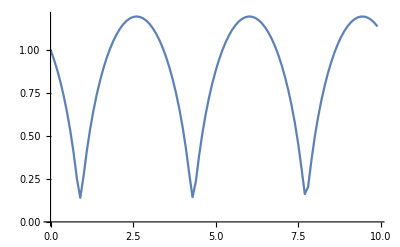

```mathematica
RK[f_,t_,x_,h_,n_]:=Module[{i,s=t,k1,k2,k3,k4,y=x,h2=N[h/2,30]},
For[i=1,i≤n,i++,
k1=h*f[y];
s=s+h2;
k2=h*f[y+(k1/2)];
k3=h*f[y+(k2/2)];
s=s+h2;
k4=h*f[y+k3];
y=y+(k1+2*k2+2*k3+k4)/6];
y]
g[x_]:={x[[2]],-x[[1]]/(x[[1]]^2+x[[3]]^2)^(3/2),x[[4]],-x[[3]]/(x[[1]]^2+x[[3]]^2)^(3/2)};

x={0,-.5,1.,-.5};

lst={};
dt=.1;
n=100;
For[t=0,t<10,t=t+dt,lst=Append[lst,{t,(x[[1]]^2+x[[3]]^2)^(1/2)}];
x=RK[g,t,x,dt/n,n]]
ListPlot[lst,Joined->True]
```

```mathematica
t=2.;
f = 100;
For[i=0,i<10,i++,
x=RK[g,0,x,t/f, f];
t = t - x[[1]]/x[[2]];
Print[t,"  ",  x]]
```

-5.96343×10^102  {9.12404×10^103,15.3,-3.25668×10^103,-5.46109}

-5.96343×10^102  {3.10827×10^88,15.3,6.51493×10^88,-5.46109}

-4.97323×10^87  {-9.12404×10^103,15.3,3.25668×10^103,-5.46109}

5.96343×10^102  {-9.12404×10^103,15.3,3.25668×10^103,-5.46109}

5.96343×10^102  {5.96788×10^87,15.3,9.10102×10^88,-5.46109}

-4.97323×10^87  {9.12404×10^103,15.3,-3.25668×10^103,-5.46109}

-5.96343×10^102  {9.12404×10^103,15.3,-3.25668×10^103,-5.46109}

-5.96343×10^102  {-2.36229×10^88,15.3,1.13638×10^89,-5.46109}

0.  {-9.12404×10^103,15.3,3.25668×10^103,-5.46109}

5.96343×10^102  {-9.12404×10^103,15.3,3.25668×10^103,-5.46109}